# Dünne Linsen

## Laplace

### Berechnung

```mathematica
b = {{1, 2, 3, 4, 5, 6, 7, 8, 9, 10}};
g = {{8, 7, 6, 5, 4, 3, 3, 2, 2, 1}};
f = 1/(1/b+1/g)//N;
Grid[{b[[1]],g[[1]],f[[1]]},Frame->All]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
8 | 7 | 6 | 5 | 4 | 3 | 3 | 2 | 2 | 1
0.888889 | 1.55556 | 2. | 2.22222 | 2.22222 | 2. | 2.1 | 1.6 | 1.63636 | 0.909091

### Graph

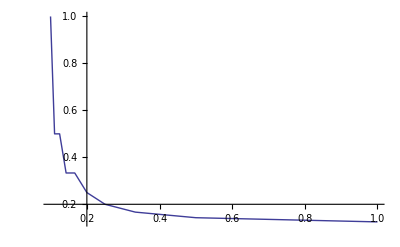

```mathematica
ListLinePlot[Table[{1/b[[1,x]],1/g[[1,x]]},{x,1,Length[b[[1]]]}]]
```